```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

## Final result on ECAL requirement

```mathematica
ECALfianl={Log[10,#1], #4} & @@@ Import[NotebookDirectory[]<>"../ECAL.csv"][[2;;]];
smallanglephoton={Log[10,#1], #2} & @@@ Import[NotebookDirectory[]<>"../ECAL.csv"][[2;;]];(*photon whose angle is small/photon who decay in volume*)
smallopenangle={Log[10,#1], #3} & @@@ Import[NotebookDirectory[]<>"../ECAL.csv"][[2;;]];(*final accetped/photon whose angle is small*)
```

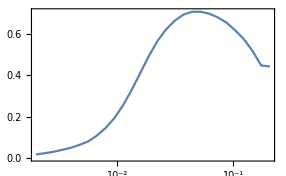

```mathematica
ListLinePlot[ECALfianl,FrameTicks->{{True,None},{myTicks[-3,0,1],None}}]
```

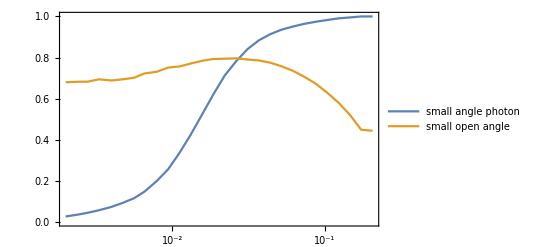

```mathematica
ListLinePlot[{smallanglephoton,smallopenangle},FrameTicks->{{True,None},{myTicks[-3,0,1],None}},PlotLegends->{"small angle photon","small open angle"}]
```

## Import data in many steps: energy, momentum, angle, and γ

### Initial dark photon

```mathematica
initial2=Import[NotebookDirectory[]<>"initial_2.csv"];
initial20=Import[NotebookDirectory[]<>"initial_20.csv"];
initial200=Import[NotebookDirectory[]<>"initial_200.csv"];
initial200g4=Import[NotebookDirectory[]<>"initial_200_g4.csv"];
```

### In volume dark photon

```mathematica
inv2=Import[NotebookDirectory[]<>"involume_2.csv"];
inv20=Import[NotebookDirectory[]<>"involume_20.csv"];
inv200=Import[NotebookDirectory[]<>"involume_200.csv"];
inv200large=Import[NotebookDirectory[]<>"involume_200_100k.csv"];
inv200g4=Import[NotebookDirectory[]<>"involume_200_g4.csv"];
```

### Generated angle for decay products in lab frame

```mathematica
thetalab2=Flatten[Log10[Import[NotebookDirectory[]<>"thetalab_2.csv"]]];
thetalab20=Flatten[Log10[ Import[NotebookDirectory[]<>"thetalab_20.csv"]]];
thetalab200=Flatten[Log10[Import[NotebookDirectory[]<>"thetalab_200.csv"]]];
thetalab200large=Flatten[Log10[Import[NotebookDirectory[]<>"thetalab_200_100k.csv"]]];
thetalab200g4=Flatten[Log10[Import[NotebookDirectory[]<>"thetalab_200_g4.csv"]]];
```

## Plots

### θ_A distribution

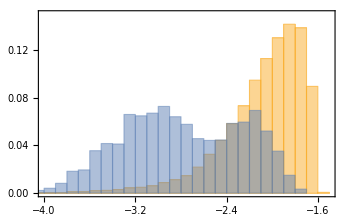

```mathematica
Histogram[{Log10[#3] & @@@ initial20,Log10[#3] & @@@ inv20},Automatic,"Probability",PlotRange->{{-4,-1.5},{0,0.15}}]
```

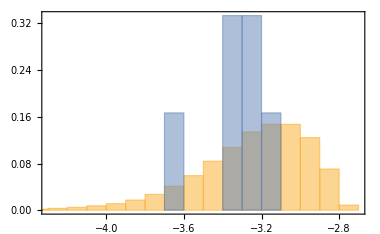

```mathematica
Histogram[{Log10[#3] & @@@ initial200,Log10[#3] & @@@ inv200},Automatic,"Probability"]
```

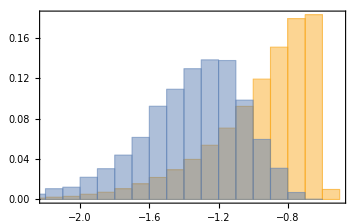

```mathematica
Histogram[{Log10[#3] & @@@ initial2,Log10[#3] & @@@ inv2},Automatic,"Probability"]
```

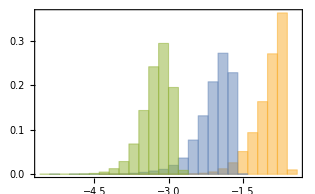

```mathematica
Histogram[{Log10[#3] & @@@ initial2,Log10[#3] & @@@ initial20,Log10[#3] & @@@ initial200},Automatic,"Probability"]
```

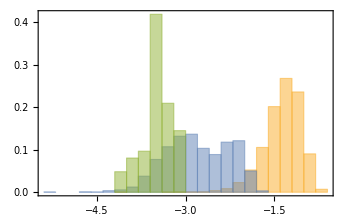

```mathematica
Histogram[{Log10[#3] & @@@ inv2,Log10[#3] & @@@ inv20,Log10[#3] & @@@ inv200large},Automatic,"Probability"]
```

### γ factor distribution

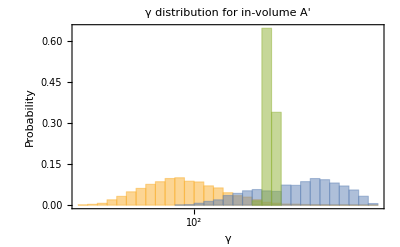

```mathematica
Histogram[{Log10[#4] & @@@ inv2,Log10[#4] & @@@ inv20,Log10[#4] & @@@ inv200large},30,"Probability",FrameTicks->{{True,None},{myTicks[0,5,1],None}},BaseStyle->{FontSize->14,FontFamily->"Times"},Frame->True,FrameLabel->{"γ","Probability"},LabelStyle->{Black},PlotLabel->Style["γ distribution for in-volume A'",FontFamily->"Times",FontSize->16],Epilog->{Inset[Framed[Column[{SwatchLegend[{Directive[ColorData[97,2],Opacity[0.5]],Directive[ColorData[97,1],Opacity[0.5]],Directive[ColorData[97,3],Opacity[0.5]]},{Style["m_A' = 2 MeV", FontFamily->Times,FontSize->10],Style["m_A' = 20 MeV",FontFamily->Times,FontSize->10],Style["m_A' = 200 MeV",FontFamily->Times,FontSize->10]}]}],RoundingRadius->5],Scaled[{0.85,0.78}]] },ImageSize->400]
```

### Opening angle distribution, theory vs simulation

```mathematica
openee200large=Import[NotebookDirectory[]<>"openee_200_100k.csv"];
```

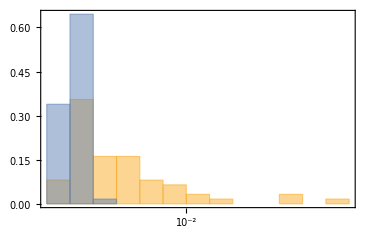

```mathematica
Histogram[{Flatten[Log10[openee200large]],Log10[2*#4^-1] & @@@ inv200large},Automatic,"Probability",FrameTicks->{{True,None},{myTicks[-3,1,1],None}}]
```

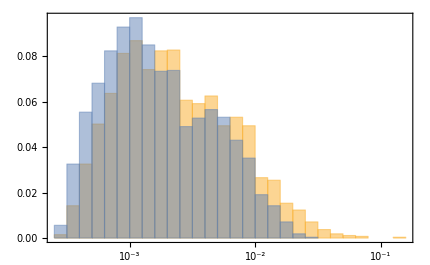

```mathematica
openee20=Import[NotebookDirectory[]<>"openee_20.csv"];
Histogram[{Flatten[Log10[openee20]],Log10[2*#4^-1] & @@@ inv20},Automatic,"Probability",FrameTicks->{{True,None},{myTicks[-3,1,1],None}}]
```

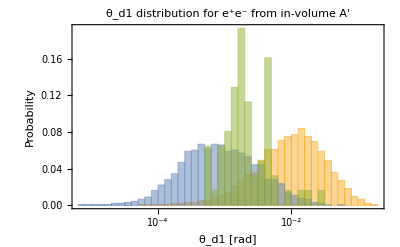

```mathematica
Histogram[{thetalab2,thetalab20,thetalab200large},50,"Probability",FrameTicks->{{True,None},{myTicks[-6,1,1],None}},PlotLabel->"θ_d1 distribution for e^+e^- from in-volume A'",BaseStyle->{FontSize->14,FontFamily->"Times"},Frame->True,FrameLabel->{"θ_d1 [rad]","Probability"},LabelStyle->{Black},Epilog->{Inset[Framed[Column[{SwatchLegend[{Directive[ColorData[97,2],Opacity[0.5]],Directive[ColorData[97,1],Opacity[0.5]],Directive[ColorData[97,3],Opacity[0.5]]},{Style["m_A' = 2 MeV", FontFamily->Times,FontSize->10],Style["m_A' = 20 MeV",FontFamily->Times,FontSize->10],Style["m_A' = 200 MeV",FontFamily->Times,FontSize->10]}]}],RoundingRadius->5],Scaled[{0.85,0.78}]] },ImageSize->400]
```

### Change coupling in sample directly: will that change?

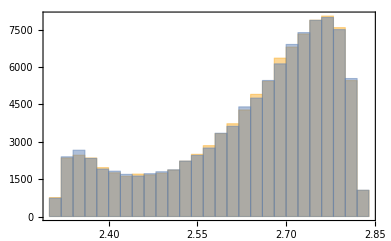

```mathematica
Histogram[{Log10[#4] & @@@ initial200,Log10[#4] & @@@ initial200g4}]
```

Exactly the same! So we can simply use the unified coupling to generate samples, then use any coupling for calculation.